# Robotics Project

Mariangela Menolotto
Stefano Maugeri
Visualization trajectory

```mathematica
Clear["Global`*"]
```

```mathematica
egoParameters={L->0.379,r->0.13,m->21.,mc->17.9,mr->1.6,ml->1.6,l->0.248,g->9.81};
```

egoP

-Graphics3D-

## Rotation Matrix

```mathematica
Rsb[θ_]:=RotationMatrix[θ,{0,0,1}];
Rsbnegativa[θ_]:=RotationMatrix[-θ,{0,0,1}];
Rbc[ϕ_]:=RotationMatrix[ϕ, {1,0,0}];
Rbcnegativa[ϕ_]:=RotationMatrix[-ϕ, {1,0,0}];
Rsi[α_]:=RotationMatrix[α, {1,0,0}];
```

```mathematica
Rcr[θi_]:=RotationMatrix[θi, {1,0,0}];
```

```mathematica
Transpose[Rbc[ϕ]].Transpose[Rsb[θ]].Transpose[Rsi[α]]//FullSimplify//MatrixForm;
```

## Visualization Functions Declaration

### Angles Parse

```mathematica
radToDeg[angle_]:=angle/Degree;
degToRad[angle_]:=angle Degree;
```

### Dynamics Plots

```mathematica
plotResults[rulesSolution_,integrationParameters_]:=Module[{},
GraphicsGrid[
{
{
Plot[x[t]/.rulesSolution,{t,0,timeOfSimulation}, PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["x(t)\n(m)",FontSize->18]},RotateLabel->False],
Plot[y[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["y(t)\n(m)",FontSize->18]},RotateLabel->False]
},
{
Plot[1/Degree θ[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ(t)\n(deg)",FontSize->18]},RotateLabel->False],
Plot[1/Degree ϕ[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ(t)\n(deg)",FontSize->18]},RotateLabel->False]
},
{
Plot[1/Degree θr[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θr(t)\n(deg)",FontSize->18]},RotateLabel->False],
Plot[1/Degree θl[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θl(t)\n(deg)",FontSize->18]},RotateLabel->False]
}
,
{
Plot[1/Degree ν2[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["θ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False],
Plot[1/Degree ν3[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ϕ̇(t)\n(deg/s)",FontSize->18]},RotateLabel->False]
},
{
Plot[ν1[t]/.rulesSolution,{t,0,timeOfSimulation},PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style["ν1\n(m/s)",FontSize->18]},RotateLabel->False]
}
},Frame->All,Spacings->Scaled[0.15],PlotLabel->Style[{radToDeg[α],τlx,τrx}/.integrationParameters,FontSize->18]
]
]
```

### Environment and Robot Build

#### Axes and Slope

```mathematica
centerAxes := {0,0,0};
limitAxes[par_,α_]:=PlotRange->{{-0.2,3+0.2},{-0.2,par+0.2},{-0.3,0.3par+10α/(Pi/2)}};
xversor[par_]:={Thickness[.005],Arrow[{centerAxes,{par,0,0}}]};
yversor[par_]:={Thickness[.005],Arrow[{centerAxes,{0,par,0}}]};
zversor[par_]:={Thickness[.005],Arrow[{centerAxes,{0,0,par}}]};
versor[par_]:={xversor[par],yversor[par],zversor[par]};
```

```mathematica
xversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["x",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{lengthVersor,0,0}+{0,0,2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{lengthVersor,0,0}}]
};
yversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["y",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,lengthVersor,0}+{0,0,2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,lengthVersor,0}}]
};
zversorM[xor_,yor_,zor_,α_,θ_,ϕ_,color_,lengthVersor_]:={
Text[Style["z",FontSize->15,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,lengthVersor}+{0,0,2}],
color,
Thickness[.001],
Arrow[{{xor,yor,zor},{xor,yor,zor}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,lengthVersor}}]
};
```

```mathematica
computeZ2[y_,α_,rad_]:=Rsi[α].{0,0,rad};
```

```mathematica
versorMoved[{xor_,yor_,zor_},α_,θ_,ϕ_,text_,xlab_,ylab_,zlab_,color_,lengthVersor_]:={
Text[Style[text,FontSize->20,Bold,FontColor->color],{xor,yor,zor}+Rsi[α].Rsb[θ].{xlab,ylab,zlab}],
xversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor],
yversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor],
zversorM[xor,yor,zor,α,θ,ϕ,color,lengthVersor]
};
```

```mathematica
rampa[scale_, α_]:={Polygon[{{0,0,0},{scale 6,0,0},{scale 6,scale 10 Cos[α],scale 10Sin[α]},{0,scale 10 Cos[α],scale 10 Sin[α]}}]}
```

```mathematica
rampaCol[scale_, α_,color_]:={color,Polygon[{{0,0,0},{6,0,0},{6,10 Cos[α],10 Sin[α]},{0,10 Cos[α], 10 Sin[α]}}]}
```

```mathematica
rampa[scale_, α_,color_,yego_]:={color,Polygon[{{0,0+yego,0},{scale,0+yego,0},{scale,scale Cos[α]+yego,scale Sin[α]},{0,scale Cos[α]+yego, scale Sin[α]}}]}
```

```mathematica
startLine[shiftX_,shiftY_,genScale_,α_]:={Green, Thickness[0.005],Line[
{
RotationMatrix[α,{1,0,0}].{xMatlab[[1]]-1+shiftX,yMatlab[[1]]+shiftY,0},
RotationMatrix[α,{1,0,0}].{xMatlab[[1]]+1+shiftX,yMatlab[[1]]+shiftY,0}
}]}
```

#### Robot parts

```mathematica
baseEgo:=2 l /.egoParameters;
radiuswheel:=r/.egoParameters;
heightCM:=L/.egoParameters;
heightEGO:=1;
radiusSphere:=0.08;
```

```mathematica
wheelr[x_,y_,z_,θ_,α_,r_]:=Cylinder[{{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2,0,0},{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}},r];
wheell[x_,y_,z_,θ_,α_,r_]:=Cylinder[{{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2,0,0},{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}},r];
base[x_,y_,z_,θ_,ϕ_,α_]:={Thickness[.01],Line[{{x,y,z}-Rsi[α].Rsb[θ].Rbc[ϕ].{baseEgo/2,0,0},{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{baseEgo/2,0,0}}]};
pendulum[x_,y_,z_,θ_,ϕ_,α_]:={Thickness[.01],Line[{{x,y,z},{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,heightEGO}}]};
radiusR[x_,y_,z_,θ_,ϕ_,θr_,α_,r_]:={Thickness[.005],Red,Line[{{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0},{x,y,z}+Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}+Rsi[α].Rsb[θ].Rbc[ϕ].Rcr[θr].{0,0,r}}]}
radiusL[x_,y_,z_,θ_,ϕ_,θl_,α_,r_]:={Thickness[.005],Red,Line[{{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0},{x,y,z}-Rsi[α].Rsb[θ].{baseEgo/2+0.02,0,0}+Rsi[α].Rsb[θ].Rbc[ϕ].Rcr[θl].{0,0,r}}]}
computeZ[y_,α_,r_]:=r/Cos[α]+y Tan[α];
drawCM[x_,y_,z_,θ_,ϕ_,α_,radSphere_]:=Sphere[{{x,y,z}+Rsi[α].Rsb[θ].Rbc[ϕ].{0,0,heightCM}},radSphere]
```

#### Robot

```mathematica
ego[x_,y_,θ_,ϕ_,θr_,θl_,α_]:={(*All the angles are in rad*)
base[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α],
wheell[x,y,computeZ[y,α,radiuswheel],θ,α,radiuswheel],
wheelr[x,y,computeZ[y,α,radiuswheel],θ,α,radiuswheel],
radiusR[x,y,computeZ[y,α,radiuswheel],θ,ϕ,θr,α,radiuswheel],
radiusL[x,y,computeZ[y,α,radiuswheel],θ,ϕ,θl,α,radiuswheel],
drawCM[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α,radiusSphere],
pendulum[x,y,computeZ[y,α,radiuswheel],θ,ϕ,α]
}
```

```mathematica
egoP:=Graphics3D[
{
ego[0, 0,0,0,0,0,0],
Text[Style["CM",FontSize->15,Bold,FontColor->Black],{0,0,heightCM+radiuswheel}],
(*Sphere[{0,0,heightCM+radiuswheel},0.001],*)
{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0.07,0,radiuswheel},{0.07,0,radiuswheel+heightCM}}]}, Text[Style["L",FontSize->15,Bold,FontColor->Black],{0.1,0,radiuswheel+heightCM/2}]},

{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0,0,radiuswheel+0.04},{-baseEgo/2-0.004,0,radiuswheel+0.04}}]}, Text[Style["l",FontSize->15,Bold,FontColor->Black],{-baseEgo/4-3/2*0.01,0,radiuswheel+0.08}]},

{Thickness[0.003], {Arrowheads[{-0.03,0.03}],Arrow[{{0.05-baseEgo/2-0.03,0,radiuswheel},{0.05-baseEgo/2-0.03,0,0}}]}, Text[Style["r",FontSize->15,Bold,FontColor->Black],{0.05-baseEgo/2-0.03,-0.05,0.04+radiuswheel/2}]},

Text[Style["mc",FontSize->15,Bold,FontColor->Black],{-0.05,0,heightCM/2+radiuswheel}],
Text[Style["ml",FontSize->15,Bold,FontColor->Black],{-baseEgo/2-0.08,-radiuswheel-0.01,radiuswheel}],
Text[Style["mr",FontSize->15,Bold,FontColor->Black],{+baseEgo/2+0.08,radiuswheel+0.01,0.05+radiuswheel}]

}/.egoParameters

,Boxed->False,Axes->False
]
```

### Simulator 3D Graphics - Dynamics

```mathematica
showEgoDynamicSolved[αα_,τrxvar_,τlxvar_]:=Module[{},
solEgoDyn2=computeQuasiVelocities[αα,τrxvar,τlxvar];
Return[{
Manipulate[
Column[{
Grid[{
{"α: ",radToDeg[α]/.{α->αα}},
{"τr, τl: ",{τrx,τlx}/.{α->αα,τlx->τlxvar,τrx->τrxvar}},
{"ϕ[0]",radToDeg[ϕ[0]]/.solEgoDyn2},
{"θ[0]",radToDeg[θ[0]]/.solEgoDyn2}
}
],
Graphics3D[{
versor[scale/5],
rampa[scale,αα],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
ego[x[tt]+5/2, y[tt]+scale 3/4,θ[tt], ϕ[tt],θr[tt],θl[tt],α/.{α->αα,τlx->τlxvar,τrx->τrxvar}]/.solEgoDyn2 (*Modellizzazione del robot, le coordinate si riferiscono al centro della base*)

},limitAxes[scale,αα],Axes->True,ImageSize->setIimageSize,Boxed->True
]
},Alignment->Center
],
{{scale,5, "Area size"},2,15,1,Appearance->{"Labeled"}},
{{tt,0,"Time t (sec)"},0,timeOfSimulation,Appearance->{"Labeled", "Open"},AnimationRate->1}
(*,ContentSize->{800,600}*)
],
plotResults[ solEgoDyn2,{α->αα,τrx->τrxvar,τlx->τlxvar}]
}]
];
```

### Simulator 3D Graphics - Statics

#### Definizione coppie nella grafica 3D

```mathematica
arrowτr[x_,y_,θ_,α_,τrx_]:={Thickness[0.01],LightBlue,Arrow[{{x,y,computeZ[y,α,radiuswheel]}+Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0},  {x,y,computeZ[y,α,radiuswheel]}+Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0} +    Rsi[α].Rsb[θ].{τrx,0,0} }]}
arrowτl[x_,y_,θ_,α_,τlx_]:={Thickness[0.01],LightBlue,Arrow[{{x,y,computeZ[y,α,radiuswheel]}-Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0},  {x,y,computeZ[y,α,radiuswheel]}-Rsi[α].Rsb[θ].{baseEgo/2+2+5,0,0} +    Rsi[α].Rsb[θ].{τlx,0,0} }]}
```

#### Definizione funzione di visualizzazione 3D

```mathematica
showEgoStaticSolved[α_,ϕ_,θ_,μ_,scale_]:=Module[{},
Return[{
Column[{
Grid[{
{"{τlx, τrx}",{τlx,τrx}}
}
],
Graphics3D[{
versor[scale/5],
rampa[scale,α],  (*Superficie in cui sta ego, il primo parametro è la larghezza, il secondo l'angolo*)
ego[5/2,scale/2,θ, ϕ,τrx,τlx,α],  (*Modellizzazione del robot, le coordinate si riferiscono al centro della base*)
arrowτr[scale/2,scale/2,θ,α,Clip[τrx,{-300,300}]],
arrowτl[scale/2,scale/2,θ,α,Clip[τlx,{-300,300}]]

},limitAxes[scale ,α],Axes->True,ImageSize->800
]
}/.solverForcesStaticEquation[α,ϕ,θ,μ]/.egoParameters,Alignment->Center
]
}]
]
```

# Robot Simulator - Data From Matlab

### Import .dat files

```mathematica
SetDirectory[ NotebookDirectory[]];
```

```mathematica
directoryMatlab:="ego_export\\";
```

```mathematica
setIimageSize=Medium;
```

```mathematica
importData:={
xMatlab=Transpose[Import[StringJoin[directoryMatlab,"x.dat"]]]//Flatten;
yMatlab=Transpose[Import[StringJoin[directoryMatlab,"y.dat"]]]//Flatten;
θMatlab=Transpose[Import[StringJoin[directoryMatlab,"theta.dat"]]]//Flatten;
ϕMatlab=(Transpose[Import[StringJoin[directoryMatlab,"phi.dat"]]]//Flatten);
θrMatlab=Transpose[Import[StringJoin[directoryMatlab,"thetar.dat"]]]//Flatten;
θlMatlab=Transpose[Import[StringJoin[directoryMatlab,"thetal.dat"]]]//Flatten;
ν1Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu1.dat"]]]//Flatten;
ν2Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu2.dat"]]]//Flatten;
ν3Matlab = Transpose[Import[StringJoin[directoryMatlab,"nu3.dat"]]]//Flatten;
ν1IntMatlab = Transpose[Import[StringJoin[directoryMatlab,"nu1int.dat"]]]//Flatten;
τrMatlab = Transpose[Import[StringJoin[directoryMatlab,"taur.dat"]]]//Flatten;
τlMatlab = Transpose[Import[StringJoin[directoryMatlab,"taul.dat"]]]//Flatten;
αMatlab=Import[StringJoin[directoryMatlab,"alpha.dat"]]//Flatten;
}
```

### Analyze file

```mathematica
fileLen:=xMatlab//Dimensions//First
```

```mathematica
θzero:=θMatlab[[1]];
ϕzero:=ϕMatlab[[1]];
```

### Declaration Functions

#### Plot

```mathematica
singlePlot[signal_,label_]:=ListLinePlot[Transpose[{Range[fileLen],signal}], PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time (s)",FontSize->14],Style[label,FontSize->18]},RotateLabel->False,PlotRange->All
,FrameTicks->{{Automatic,Automatic}(*,{{{0,"0"},{100,"10"},{200,"20"},{50,"5"},{150,"15"}},None}*)}
]
```

```mathematica
circle[signal_,t_,radiusX_,radiusY_]:={Red,Disk[{Range[fileLen][[t]],xMatlab[[t]]},{radiusX,radiusY}]}
```

```mathematica
plotResults[x_,y_,θ_,ϕ_,θr_,θl_,ν1_,ν2_,ν3_,ν1int_,τr_,τl_]:=Module[{},
GraphicsGrid[
{
{
singlePlot[x,"x(t)\n(m)"],
singlePlot[y,"y(t)\n(m)"],
singlePlot[radToDeg[θ],"θ(t)\n(deg)"]
},
{
singlePlot[radToDeg[ϕ],"ϕ(t)\n(deg)"],
singlePlot[radToDeg[θr],"θr(t)\n(deg)"],
singlePlot[radToDeg[θl],"θl(t)\n(deg)"]
},
{
singlePlot[ν1,"ν1(t)\n(m/s)"],
singlePlot[radToDeg[ν2],"θ̇(t)\n(deg/s)"],
singlePlot[radToDeg[ν3],"ϕ̇(t)\n(deg/s)"]
},
{
singlePlot[τr,"τr(t)\n(N*m)"],
singlePlot[τl,"τl(t)\n(N*m)"],
singlePlot[ν1int,"∫ν1(t)\n(m)"]
}
},Frame->All,Spacings->Scaled[0.15],PlotLabel->Style[{"α(0)=",radToDeg[αMatlab[[1]]],"°"},FontSize->18]
]
]
```

#### 3D Simulator

```mathematica
showEgoDynamicFromMatlab:=Module[{},
importData;
Return[{

Manipulate[{
Column[{
Grid[{
{StringJoin["Slope: ",ToString[radToDeg[αMatlab[[tt]]]//Chop],"°"]},
{StringJoin["Initial pitch: ",ToString[radToDeg[ϕzero]],"°"]},
{StringJoin["Initial yaw: ",ToString[radToDeg[θzero]],"°"]}
}
],
Graphics3D[{
versor[2],
If[αMatlab[[tt]] > 0,rampaCol[scale,0,Red]],
rampa[scale,αMatlab[[tt]]],
ego[
xMatlab[[tt]]+(RotationMatrix[αMatlab[[1]],{1,0,0}].{ shiftX+3,shiftY+1,0})[[1]],
yMatlab[[tt]]+(RotationMatrix[αMatlab[[1]],{1,0,0}].{ shiftX+3,shiftY+1,0})[[2]],
θMatlab[[tt]], 
ϕMatlab[[tt]],
θrMatlab[[tt]],
θlMatlab[[tt]],
αMatlab[[tt]]
]
,startLine[shiftX+3,shiftY+1,scale,αMatlab[[tt]]]
(*ego[xMatlab[[tt]]+2.5, yMatlab[[tt]]+scale 2/4,degToRad[0],degToRad[20],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab]*)
(*,
ego[xMatlab[[tt]]+1.5, yMatlab[[tt]]+scale 2/4,degToRad[0], degToRad[23],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab],
ego[xMatlab[[tt]]+3.5, yMatlab[[tt]]+scale 2/4,degToRad[0], -degToRad[23],θrMatlab[[tt]],θlMatlab[[tt]],αMatlab]
*)
}(*limitAxes[scale,αMatlab]*),Axes->True,ImageSize->800,Boxed->False,ViewPoint->{4, -2, 1.3}
]
},Alignment->Center
]
}
,
{{scale,1, "Scale"},1,3,0.01,Appearance->{"Labeled"}},
{{shiftX,0, "Shift x"},-5,5,1,Appearance->{"Labeled"}},
{{shiftY,0, "Shift y"},-5,5,1,Appearance->{"Labeled"}},
{{tt,1,"Time t (100*s)"},1,fileLen,1,Appearance->{"Labeled", "Open"},AnimationRate->1000,RefreshRate->60}
(*,ContentSize->{800,600}*)
],
plotResults[xMatlab,yMatlab,θMatlab,ϕMatlab,θrMatlab,θlMatlab,ν1Matlab,ν2Matlab,ν3Matlab,ν1IntMatlab,τrMatlab,τlMatlab]
}
]];
```

### Visualization

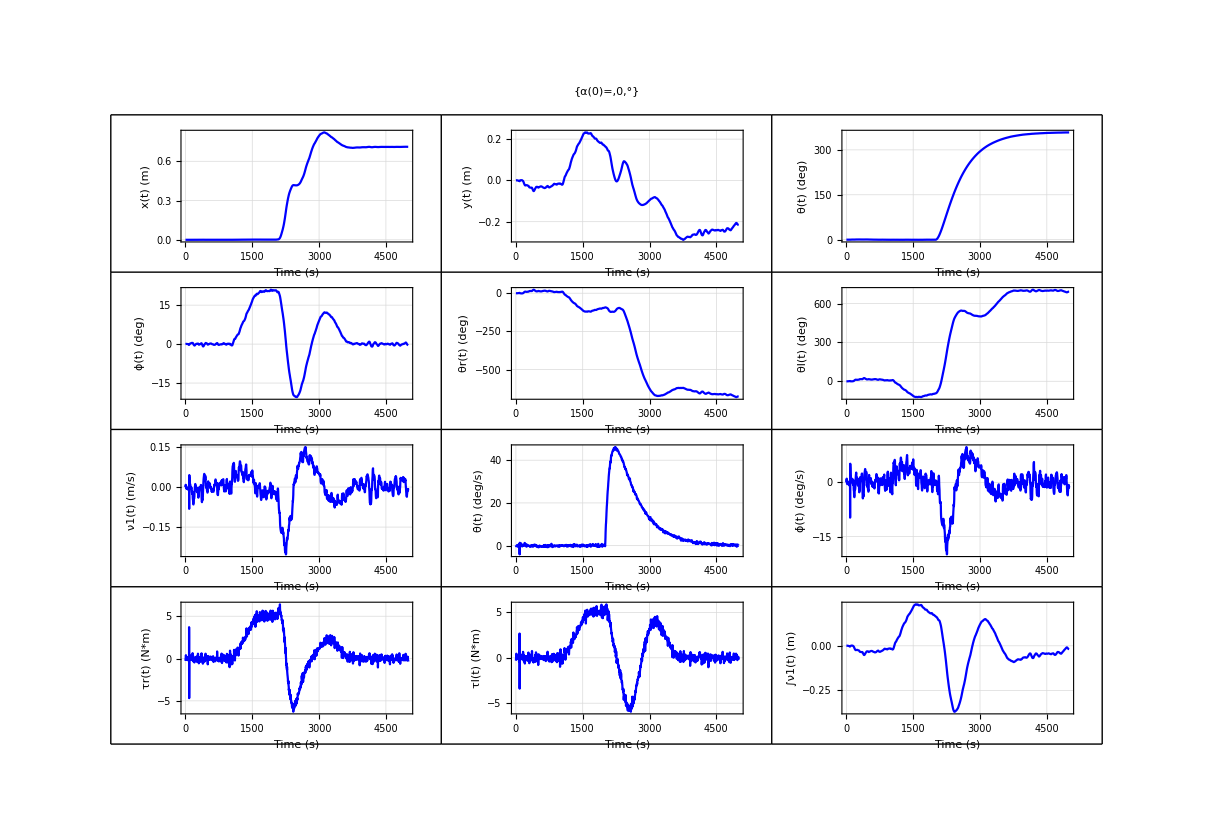

```mathematica
showEgoDynamicFromMatlab
```